## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[4];
```

## Utility Functions

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

cDiffCoeffs={1,-2,1};

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,SEDict_]:=Module[{xg,n,m, h, u1V, matV},
xg=xgrid[SEDict][[2;;-1]];
n=SEDict["n"];
m=SEDict["m"];
h =SEDict["h"];

u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

## Solve Schrodinger equation

```mathematica
SchrEqOfV[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams, SEDict];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]],Method->"Banded"]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
TofV[k_,x1_,x2_,SEsol1_,SEsol2_]:=Module[{},
Exp[I*Sqrt[2]*k*x2]*(1-Exp[-I*2*Sqrt[2]*k*(x2-x1)])/
(SEsol2-SEsol1*Exp[-I*Sqrt[2]*k*(x2-x1)])
];
```

```mathematica
TofVVec[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=
Module[{step,solk,xgf,x1,x2,Tk},
step=SEDict["TCalcStep"];
solk=SchrEqOfV[V,VParams,SEDict,kVec,D2,EMatrixVector,yVector];
xgf=xgridFull[SEDict];
x1=xgf[[1]];
x2=xgf[[step]];

Tk=Table[{
sol[[1]], 
TofV[sol[[1]],x1,x2, sol[[2,1]],sol[[2,step]]]
},
{sol,solk}];

Return[Tk];
]
```

## Define Cost Function

```mathematica
Cost[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},

(*Calculate the cost function*)
cost = Sum[
weights[[i]]*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}] /
 Sum[weights[[i]],{i,1,Length[T]}] ;
Return[cost];
];
```

```mathematica
CostTemp[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},
temp=SEDict["temp"];

(*Calculate the cost function*)
cost = Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi))*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}]/
Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi)),{i,1,Length[T]}] ;

Return[cost];
];
```

```mathematica
CostConstraint[ErrFunc_, Vpars_,SEDict_]:=Module[{alpha},
alpha=SEDict["alpha"];
alpha * ErrFunc[Vpars,SEDict]
]
```

## Search for the potential

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,costFunction_,d2_,eMatrix_,yvec_,weights_:Table[1,{i,1,Length[TGoal_]}]]:=
Module[{tvec,cost,PlotA,PlotB},
tvec=TofVVec[Vfunc, Vpars,SEDict,kVec,d2,eMatrix,yvec];
cost=costFunction[Abs[tvec], TGoal, SEDict,weights];

(*ALERT: very bad programming!!!*)
If[cost≠lastCost,
Print["Cost: ", cost];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[tvec]},PlotRange->All,PlotLabel->"Cost: "<>ToString[cost]];

Print[GraphicsRow[{PlotA,PlotB}, ImageSize->Large]]
];

lastCost=cost;
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, costFunction_,errFunction_,
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{
"DifferentialEvolution", 
"Tolerance"->0.1,
"PostProcess"->False,
"PenaltyFunction"->Function[{d,i},d*10^(2)], 
"ScalingFactor"->0.75,
 "CrossProbability"->0.5,
"RandomSeed"->3
}
]:=
Module[{VparsFlat, soln,d2mat,emat,yyvec,lastCost},
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

lastCost=1000;

soln=NMinimize[{
Hold[
costFunction[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], TGoal,SEDict,weights]+
CostConstraint[errFunction, Vpars,SEDict]
],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,costFunction,d2mat,emat,yyvec,weights]]]
];

Return[soln];
]
```

## Define actual search parameters and potentials

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

```mathematica
VGaussL2Err[params_,SEDict_]:=Module[{pot,A,x0,σ,a,b,Vout},
A=params[[1]];
x0=params[[2]];
σ=params[[3]];
a=SEDict["a"];
b=SEDict["b"];

Vout=√(π/2) A √σ (Erfc[(-a+x0)/(√2 √σ)]+Erfc[(b-x0)/(√2 √σ)]);

Return[Abs[Vout]^2];
];
```

```mathematica
VGaussL2ErrN[params_,SEDict_]:=Module[{pot},
pot=Sum[VGaussL2Err[pars,SEDict],{pars,params}];
Return[pot];
];
```

```mathematica
SEDict = Association["a"->-10, "b"->10,"n"->500,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->300, "TCalcStep"->25, "temp"->0.5, "alpha"->10];
SEDict["h"]=(SEDict["b"]-SEDict["a"])/SEDict["n"];
kgrid = kGrid[SEDict];
```

```mathematica
VGaussL2ErrN[{{1,-2,1.5},{-2,5,3}},SEDict]
```

0.000285588

## “k=1 single-comb” 3 gaussians

### Define target T-profile and weights:

```mathematica
TFunc[k_,a_,b_]:=(1+(k-a)^2/b^2)^(-1)
```

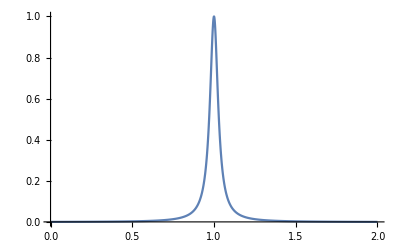

```mathematica
a=1;b=0.03;
Plot[TFunc[k,a,b],{k,0,2}, PlotRange->Full]
```

```mathematica
TTarget=Table[{k,TFunc[k,a,b]},{k,kgrid}];
```

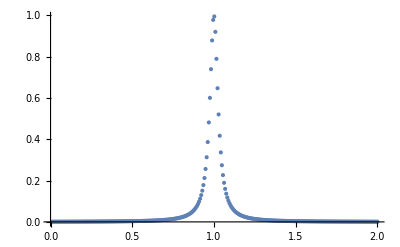

```mathematica
ListPlot[TTarget,PlotRange->Full]
```

```mathematica
kWeights=Table[BackgroundWeights[k]+TFunc[k,a,b],{k,kgrid}]^4;
```

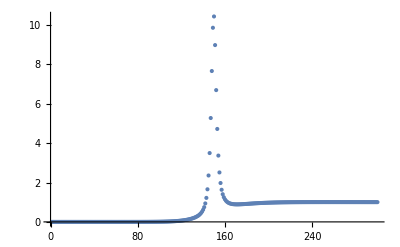

```mathematica
ListPlot[kWeights,PlotRange->All]
```

Cost: 0.574529

Params: {{0.435652,-0.0678821,0.0752711},{0.311408,0.53686,0.998003},{0.927784,-0.468978,0.313804}}

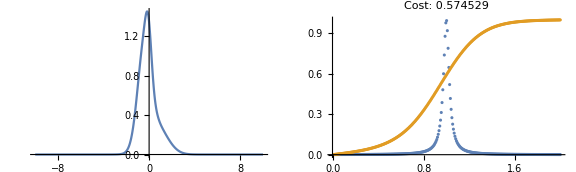

Cost: 0.49487

Params: {{-0.0602147,-1.17972,0.352382},{1.91156,0.2153,0.0959529},{0.206661,0.964419,1.18652}}

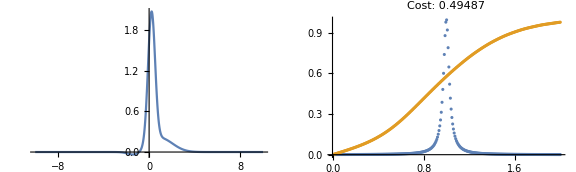

Cost: 0.34298

Params: {{0.833921,0.761391,1.93375},{1.95795,-1.0299,0.764138},{1.39364,0.268505,1.44365}}

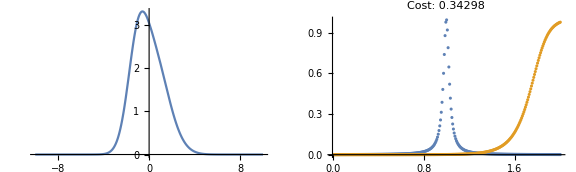

Cost: 0.212584

Params: {{-1.3482,-1.0939,1.06368},{3.02566,0.20551,1.37282},{2.74431,0.888394,1.31524}}

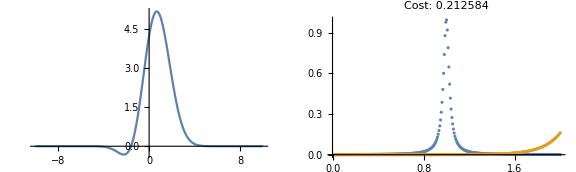

Cost: 0.212339

Params: {{0.465278,-0.309042,1.32959},{2.55691,0.342744,0.7809},{2.44518,-0.0337019,1.50107}}

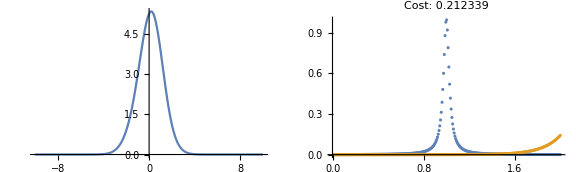

Cost: 0.211429

Params: {{1.92104,-0.0756531,0.0988458},{3.8674,-0.117813,1.53629},{1.76832,0.193466,2.41349}}

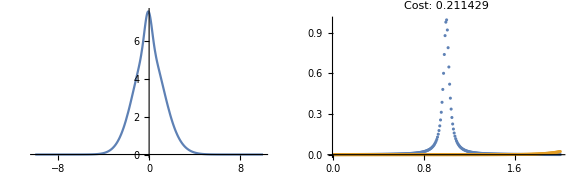

Cost: 0.21094

Params: {{0.465278,0.569394,1.32959},{5.83845,0.342744,0.7809},{-5.28494,-0.912137,0.269191}}

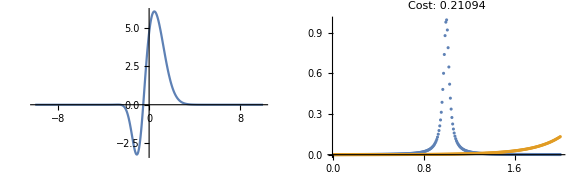

Cost: 0.210727

Params: {{-2.26847,2.88982,1.35916},{8.10317,-0.717527,0.428477},{-0.16137,-2.1723,0.0194782}}

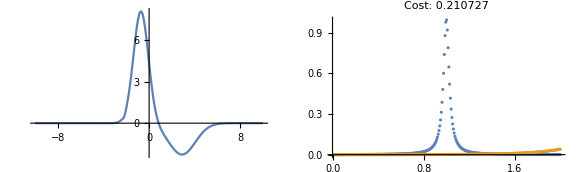

Cost: 0.178049

Params: {{0.959459,-1.71774,0.610022},{6.35678,0.580231,0.0164592},{8.95099,1.13751,0.0155429}}

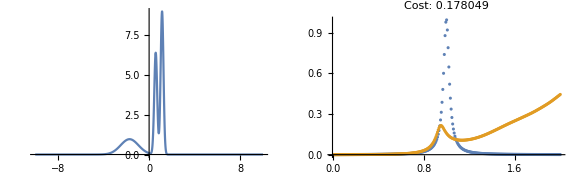

Cost: 0.116033

Params: {{5.1346,3.18606,0.0146485},{14.1818,-3.67993,0.0190245},{4.18487,0.493869,0.0123733}}

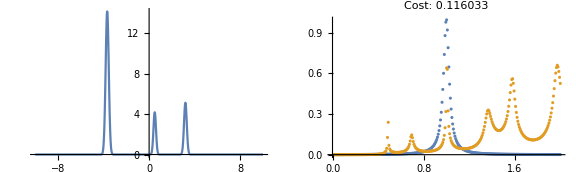

Cost: 0.101534

Params: {{-1.435,-5.62181,0.625285},{18.4525,4.4888,0.0107003},{1.19561,1.13301,2.5422}}

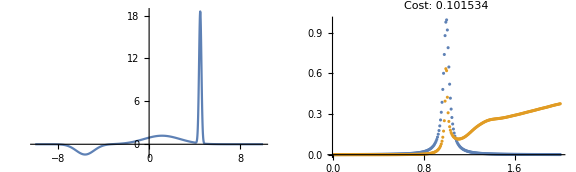

Cost: 0.101492

Params: {{0.305719,-0.0825003,1.95966},{19.3123,1.44638,0.0102377},{-11.8468,-1.36388,0.0137987}}

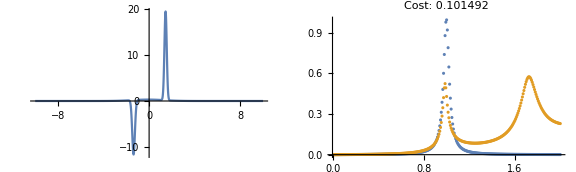

Cost: 0.064983

Params: {{10.2328,-1.37144,0.0103701},{20.6955,0.127563,0.0102192},{-2.91283,1.24388,1.58219}}

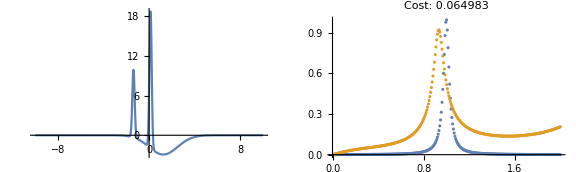

$Aborted

```mathematica
solGaussN=
SearchPotential [
TTarget,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
x01+x02+x03==0
},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
kWeights]
```

## “Low pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[0.5-k]},{k,kgrid}];
```

```mathematica
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

```mathematica
(*SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kgrid,
weightsofKGoalCool]*)
```

## “High-pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[k-0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

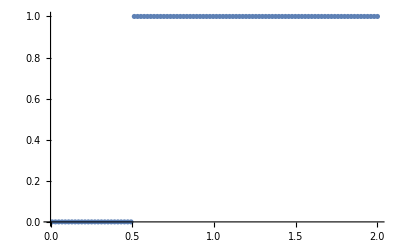

```mathematica
ListPlot[TofKGoalCool]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest]*)
```

## “Low-pass quantum filter” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[-k+0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

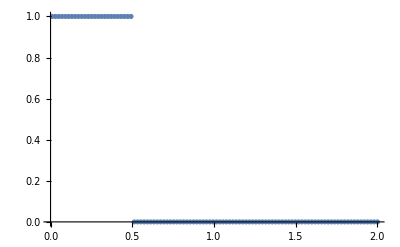

```mathematica
ListPlot[{TofKGoalCool}]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}},
{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```

## “k=0.5,1.5 double-comb” 4 gaussians, temp=0.5

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

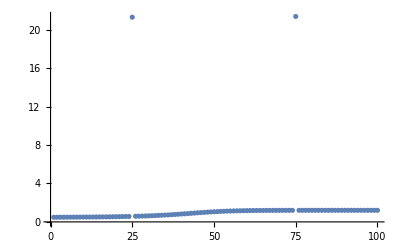

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

```mathematica
(*solGaussNTemp=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3},
{A4,x04,sigma4}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
sigma4>0.01,
x01+x02+x03+x04==0},
SEDict,
kgrid,
CostTemp,
weightsofKGoalCool]*)
```

## “k=1 single-comb” 2 gaussians, temp=infty

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/2]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/2]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

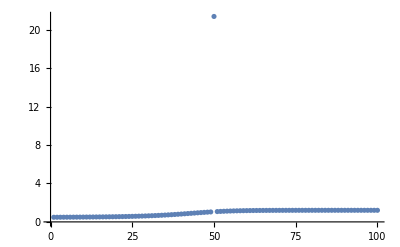

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2}},
{sigma1>0.01,
sigma2>0.01, 
x01+x02==0
},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
weightsofKGoalCool]*)
```